```mathematica
(*计算 mixing index（分母=邻域内 A 个数）*)Clear[MixingIndexA]
MixingIndexA[celldata_List,distres_:5]:=Module[{A,B,posA,posB,nearA,nearB,na,nb,ratios},(*抽取 A/B 坐标，确保是 {n,2} 的纯数值矩阵*)A=Select[celldata,#[[6]]==0&];
B=Select[celldata,#[[6]]==1&];
posA=Developer`ToPackedArray@N@A[[All,{2,3}]];
posB=Developer`ToPackedArray@N@B[[All,{2,3}]];
(*空集防护*)If[Length[posA]==0,Return[Indeterminate]];
(*建立 Nearest 查询器*)nearA=Nearest[posA];(*默认欧氏距离*)nearB=If[Length[posB]>0,Nearest[posB],({}&)];
(*一次性查询每个 A 的邻域大小（矢量化）*)na=Length/@nearA[posA,{All,distres}];
nb=If[Length[posB]>0,Length/@nearB[posA,{All,distres}],ConstantArray[0,Length[posA]]];
(*计算每个 A 的 nb/na 并取均值*)ratios=MapThread[If[#1>0,N[#2/#1],0]&,{na,nb}];
Mean[ratios]]
(*计算 mixing index（分母=邻域覆盖的格子数，含空格）*)Clear[MixingIndexAllCells]
MixingIndexAllCells[celldata_List,distres_:5,gridSize_:40]:=Module[{A,B,posA,posB,nearB,neighborhoodSize,nb,ratios},A=Select[celldata,#[[6]]==0&];
B=Select[celldata,#[[6]]==1&];
posA=Developer`ToPackedArray@N@A[[All,{2,3}]];
posB=Developer`ToPackedArray@N@B[[All,{2,3}]];
If[Length[posA]==0,Return[Indeterminate]];
(*邻域查询器（只需要B）*)nearB=If[Length[posB]>0,Nearest[posB],({}&)];
nb=If[Length[posB]>0,Length/@nearB[posA,{All,distres}],ConstantArray[0,Length[posA]]];
(*对每个 A 位置，根据边界裁剪计算邻域覆盖的格子数*)neighborhoodSize=Map[Function[{p},With[{x=p[[1]],y=p[[2]]},Total@Flatten@Table[Boole[1<=xx<=gridSize&&1<=yy<=gridSize&&EuclideanDistance[{xx,yy},{x,y}]<=distres],{xx,x-distres,x+distres},{yy,y-distres,y+distres}]]],posA];
ratios=MapThread[If[#2>0,N[#1/#2],0]&,{nb,neighborhoodSize}];
Mean[ratios]]
```

```mathematica
Intermixing={};
Do[
Do[
SetDirectory[FileNameJoin[{NotebookDirectory[],"motile-QS","Para"<>ToString@i,"mot"<>ToString@j,"celldata"}]];
cellfile=FileNames[];
time=Sort@Table[ToExpression@StringDrop[StringDrop[cellfile[[k]],10],-4],{k,1,Length@cellfile}];
mixing={};
Do[
celldata=Import[FileNameJoin[{NotebookDirectory[],"motile-QS","Para"<>ToString@i,"mot"<>ToString@j,"celldata","CellMatrix"<>ToString@time[[k]]<>".csv"}]];
mixing=Join[mixing,{MixingIndexA[celldata,5]}];
,{k,1,Length@time}];
If[Divisible[j,1]==True,Print[" Para No."<>ToString@i<>" mot No."<>ToString@j<>" finished!"]];
Intermixing=Join[Intermixing,{mixing}];
,{j,1,7}];
,{i,1,1}];
Intermixing
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Intermixing.xlsx"}],Intermixing];
```

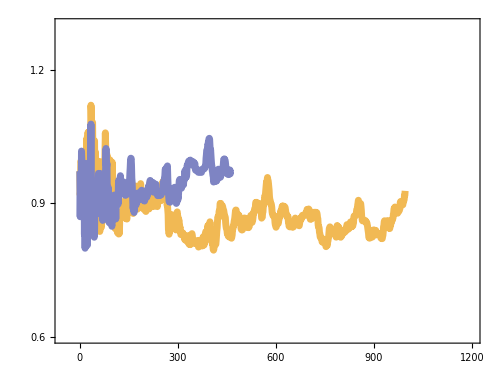

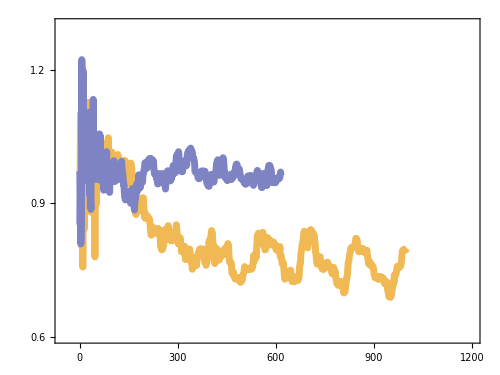

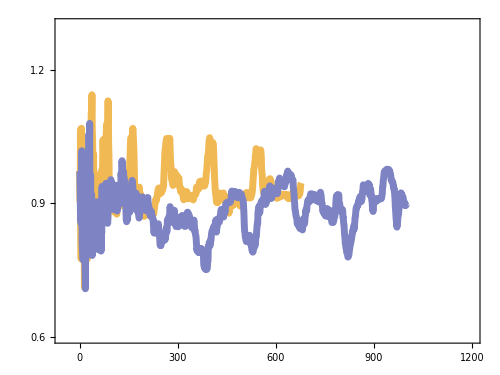

```mathematica
compare={{1,2},{3,4},{5,6}};
data=ToExpression@First@Import[FileNameJoin[{NotebookDirectory[],"Intermixing.xlsx"}]];
data=Table[DeleteCases[data[[i]],Null],{i,1,Length@data}];
plot1=ListLinePlot[{data[[1]],data[[2]]},ImageSize->500,AspectRatio->0.75,PlotRange->{{-50,1200},{0.6,1.3}},
PlotStyle->{{Directive[Thickness[0.01],RGBColor[241/255,185/255,84/255]]},{Directive[Thickness[0.01],RGBColor[126/255,132/255,195/255]]}},Frame->True,FrameStyle->Directive[Thickness[0.008],Black,30],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0.6,1.2,0.3],None},{{#,#,{0.02,0}}&/@Range[0,1200,300],None}}]
plot2=ListLinePlot[{data[[3]],data[[4]]},ImageSize->500,AspectRatio->0.75,PlotRange->{{-50,1200},{0.6,1.3}},
PlotStyle->{{Directive[Thickness[0.01],RGBColor[241/255,185/255,84/255]]},{Directive[Thickness[0.01],RGBColor[126/255,132/255,195/255]]}},Frame->True,FrameStyle->Directive[Thickness[0.008],Black,30],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0.6,1.2,0.3],None},{{#,#,{0.02,0}}&/@Range[0,1200,300],None}}]
plot3=ListLinePlot[{data[[6]],data[[5]]},ImageSize->500,AspectRatio->0.75,PlotRange->{{-50,1200},{0.6,1.3}},
PlotStyle->{{Directive[Thickness[0.01],RGBColor[241/255,185/255,84/255]]},{Directive[Thickness[0.01],RGBColor[126/255,132/255,195/255]]}},Frame->True,FrameStyle->Directive[Thickness[0.008],Black,30],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0.6,1.2,0.3],None},{{#,#,{0.02,0}}&/@Range[0,1200,300],None}}]
```

```mathematica
plotV1=Table[ListLinePlot[{Transpose@Join[{Table[j*10/60,{j,0,(Min[i,Length@data[[1]]]-1)}]},{data[[1,1;;Min[i,Length@data[[1]]]]]}],Transpose@Join[{Table[j*10/60,{j,0,(Min[i,Length@data[[2]]]-1)}]},{data[[2,1;;Min[i,Length@data[[2]]]]]}]},ImageSize->500,AspectRatio->1,PlotRange->{{-10,180},{0.6,1.3}},
PlotStyle->{{Directive[Thickness[0.01],RGBColor[241/255,185/255,84/255]]},{Directive[Thickness[0.01],RGBColor[126/255,132/255,195/255]]}},Frame->True,FrameStyle->Directive[Thickness[0.008],Black,30],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0.6,1.2,0.3],None},{{#,#,{0.02,0}}&/@Range[0,180,30],None}}],{i,1,1000}];
Export[FileNameJoin[{NotebookDirectory[],"plotV1.mp4"}],plotV1,CompressionLevel->0];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"plotV1last.tif"}],plotV1[[-1]]];
```

```mathematica
plotV2=Table[ListLinePlot[{Transpose@Join[{Table[j*10/60,{j,0,(Min[i,Length@data[[3]]]-1)}]},{data[[3,1;;Min[i,Length@data[[3]]]]]}],Transpose@Join[{Table[j*10/60,{j,0,(Min[i,Length@data[[4]]]-1)}]},{data[[4,1;;Min[i,Length@data[[4]]]]]}]},ImageSize->500,AspectRatio->1,PlotRange->{{-10,180},{0.6,1.3}},
PlotStyle->{{Directive[Thickness[0.01],RGBColor[241/255,185/255,84/255]]},{Directive[Thickness[0.01],RGBColor[126/255,132/255,195/255]]}},Frame->True,FrameStyle->Directive[Thickness[0.008],Black,30],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0.6,1.2,0.3],None},{{#,#,{0.02,0}}&/@Range[0,180,30],None}}],{i,1,1000}];
Export[FileNameJoin[{NotebookDirectory[],"plotV2.mp4"}],plotV2,CompressionLevel->0];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"plotV2last.tif"}],plotV2[[-1]]];
```

```mathematica
plotV3=Table[ListLinePlot[{Transpose@Join[{Table[j*10/60,{j,0,(Min[i,Length@data[[6]]]-1)}]},{data[[6,1;;Min[i,Length@data[[6]]]]]}],Transpose@Join[{Table[j*10/60,{j,0,(Min[i,Length@data[[5]]]-1)}]},{data[[5,1;;Min[i,Length@data[[5]]]]]}]},ImageSize->500,AspectRatio->1,PlotRange->{{-10,180},{0.6,1.3}},
PlotStyle->{{Directive[Thickness[0.01],RGBColor[241/255,185/255,84/255]]},{Directive[Thickness[0.01],RGBColor[126/255,132/255,195/255]]}},Frame->True,FrameStyle->Directive[Thickness[0.008],Black,30],Axes->False,FrameTicks->{{{#,#,{0.02,0}}&/@Range[0.6,1.2,0.3],None},{{#,#,{0.02,0}}&/@Range[0,180,30],None}}],{i,1,1000}];
Export[FileNameJoin[{NotebookDirectory[],"plotV3.mp4"}],plotV3,CompressionLevel->0];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"plotV3last.tif"}],plotV3[[-1]]];
```